## Chapter 26

```mathematica
#^2&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
Blend[{Red,#},1/2]&/@{Yellow,Green, Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
Column/@Framed@{Alphabet[][[#]],Capitalize[Alphabet[]][[#]]}&/@Range[26]
```

{a
A,b
B,c
C,d
D,e
E,f
F,g
G,h
H,i
I,j
J,k
K,l
L,m
M,n
N,o
O,p
P,q
Q,r
R,s
S,t
T,u
U,v
V,w
W,x
X,y
Y,z
Z}

```mathematica
Framed[Style[Alphabet[][[#]],RandomColor[]],Background->RandomColor[]]&/@Range[26]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}





France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
Grid[{EntityList[][[#]],EntityList[][[#]]["Flag"]}&/@Range[5], Frame->All]
```

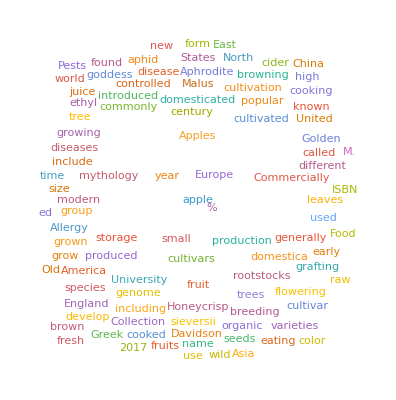
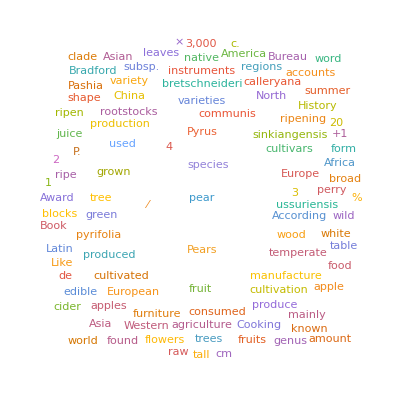
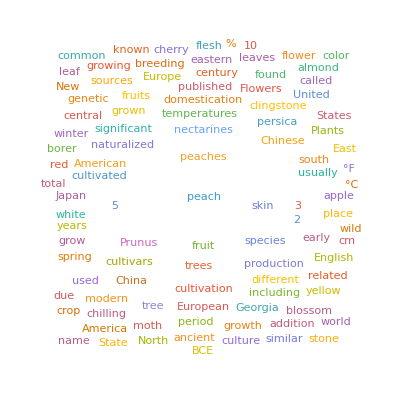

```mathematica
WordCloud[WikipediaData[#]]&/@{"apple","pear","peach"}
```

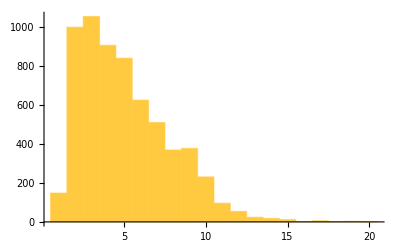
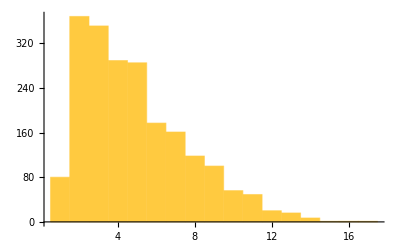
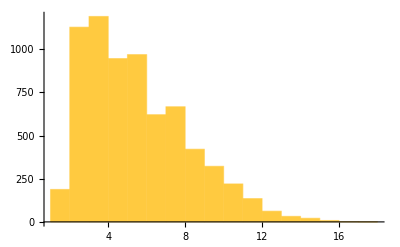

```mathematica
Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","pear","peach"}
```

```mathematica
GeoGraphics[EntityList[][[#]]]&/@Range[Length[EntityList[]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Chapter 27

```mathematica
NestList[Blur[#]&,Rasterize[Style["x",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
NestList[Rotate[Framed[#],RandomInteger[90]]&,Style["A",50],5]
```

{A,A,A,A,A,A}

```mathematica
ListLinePlot[NestList[4 #(1-#)&,0.2,100]]
```

-Graphics-

```mathematica
N[NestList[1+1/#& ,1,30][[30]]]
```

1.61803

```mathematica
NestList[3#&,1,10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
NestList[(#+2/#)/2&,1.0,5]-Sqrt[2]
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

```mathematica
NestList[[{#[[1]]+RandomReal[-1,1],#[[2]]+RandomReal[-1,1]}]&,{0,0},1000] (*no idea what's going on here*)
```

Syntax::sntxb: Expression cannot begin with "[{#[[1]]+RandomReal[-1,1],#[[2]]+RandomReal[-1,1]}]&".

```mathematica
ArrayPlot[NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]
```

Syntax::sntxf: "ArrayPlot[NestList[" cannot be followed by "Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]".

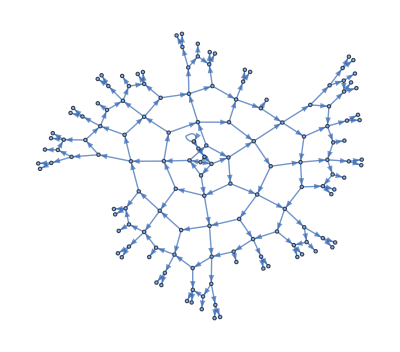

```mathematica
NestGraph[{#+1,2#}&,0,10]
```

```mathematica
NestList[GeoNearest["Country",#]&,,4]
```

GeoNearest::timeout: A network operation for GeoNearest timed out. Please try again later.

$Failed

## Chapter 28

```mathematica
123^321> 456^123
```

True

```mathematica
IntegerDigits/@Range[100]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{1,0,0}}

```mathematica
If[PrimeQ[#]==True,Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Select[WordList[],Last[Characters[#]]=="p" && First[Characters[#]]=="p"&]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,peep,penmanship,pep,pickup,pileup,pip,plop,plump,polyp,pomp,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

```mathematica
Select[Prime[Range[100]],Last[IntegerDigits[#]]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
Select[RomanNumeral[Range[100]],MemberQ[Characters[#], "I"]==False&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
Select[RomanNumeral[Range[1000]],Characters[#]==Reverse[Characters[#]]&]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
Select[IntegerName[Range[100]],First[Characters[#]]==Last[Characters[#]]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
Select[TextWords[WikipediaData["Words"]],StringLength[#]>15&]
```

{yibi-jarran-gabun,yibi-gabun-jarran,orthographically,multiple-morpheme,Proto-Indo-European,978-0-08-044854-1}

```mathematica
NestList[If[EvenQ[#]==True,#/2,3#+1 ]&,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

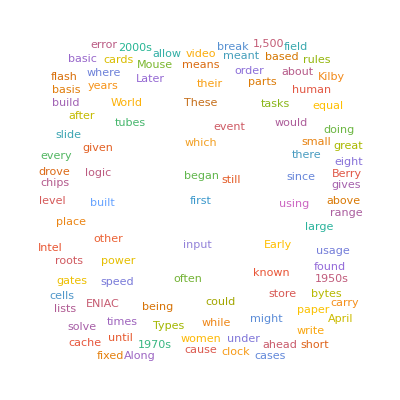

```mathematica
WordCloud[Select[TextWords[WikipediaData["Computers"]],StringLength[#]==5&]]
```

```mathematica
Select[WordList[],StringLength[#]≥3&&StringTake[#,3]==StringTake[StringReverse[#],3]&&StringReverse[#]≠#&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
Select[Select[WordList[],StringLength[#]==10&],Total[LetterNumber/@Characters[#]]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}